## Clustering using basic algorithms - K-means a DBscan

```mathematica
dataset=SemanticImport[NotebookDirectory[]<>"CC General.csv"];
data= Import[NotebookDirectory[]<>"CC General.csv"][[2;;All]];
```

## K - means

```mathematica
clusterAll[centroids_,inputData_]:=Module[{clusters},
clusters=<|#->{}&/@centroids|>;
AppendTo[clusters[Nearest[centroids,#][[1]]],#]&/@inputData;clusters
];

showClusters[centroids_,clusters_,numberOfColors_]:=Module[{colors,graph},
colors=AssociationThread[centroids,RandomColor[numberOfColors]];
graph=Graphics[{Table[{colors[m],PointSize[.025],Point@clusters[m],PointSize[.05],Point@m},{m,centroids}]},Axes->True,AspectRatio->1,PlotLabel->"Graph k-Means"];

Return@graph;
];

kMeans[inputData_, k_]:=Module[{input,centroidNumber,maxX,maxY,cX,cY,centroids={},clusters,clustersOld,counter=0, colors,graph},
clustersOld=<|#->{}&/@centroids|>;
input=inputData;
centroidNumber=k;

(* generate random positions for centroids *)
maxX=Max[inputData[[All;;,1]]];
maxY=Max[inputData[[All;;,2]]];

cX=RandomReal[{0,maxX},k];
cY=RandomReal[{0,maxY},k];

(* get 2D centroids *)
For[i=1,i<=k,i++,
AppendTo[centroids,{cX[[i]],cY[[i]]}];
];

(* for each item find nearest centroid *)
clusters=clusterAll[centroids,input];

(* construct graph *)
(*graph=showClusters[centroids,clusters];*)

(* keep recomputing (converging) until there is no change in clusters - all belong to the same one *)
While[clusters!=clustersOld,
(*Print@"Converging"; *)

(* for each centroid recompute its position (to mean of the cluster)*)
For[i=1,i<=Length@centroids,i++,
centroids[[i]]=Mean[clusters[centroids[[i]]]];
];
(*Print@centroids; *)

(* save oldClusters and then compute new ones *)
clustersOld=clusters;
clusters=clusterAll[centroids,input];
graph=showClusters[centroids,clusters,k];

counter++;
];

Print["Converged in ",counter," iterations"];
Print["Final centroids : ", centroids];

Return@graph
];
```

### a) balance (x) and purchases (y)

Converged in 29 iterations

Final centroids : {{3811.8,12736.8},{838.394,756.492},{5600.78,1126.14}}

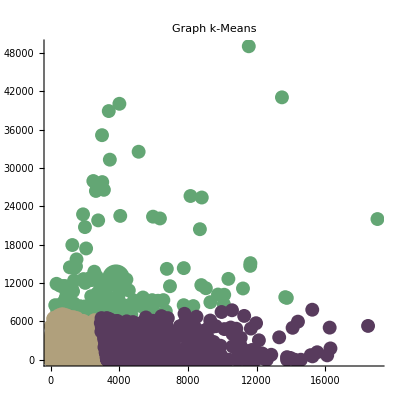

```mathematica
dataKMa=data[[All,{2,4}]];
kMeans[dataKMa,3]
```

## DBSCAN (Density-Based Spatial Clustering of Applications with Noise)

```mathematica
trainingDataDBSCAN = {{0,100}, {0,200}, {0,275},{100,150},{200,100},{250,200},{0,300},{100,200},{600,700},{650,700},{675,700},{675,710},{675,720},{50,400}};
```

```mathematica
DBSCAN[inputData_, epsilon_, minPts_] := Module[{neighbours,groupedNeighbours,clusters,flattenClusters,noisePts},
(* maybe has to be given by local variables *) 
neighbours=getNeighbours[inputData,epsilon,minPts]; 

(* groupNeighbours - get rid of mulitplicity of points *)
groupedNeighbours=groupNeighbours[neighbours];

clusters=getClusters[groupedNeighbours,minPts];
flattenClusters=Flatten[clusters,1];

(*Print["NoisePts: ", DeleteCases[inputData,Alternatives@@flattenClusters]];*)

(* show clusters in 2D *)
ListPlot[clusters,AspectRatio->1,Axes->True,PlotLabel->"Graph DBSCAN"]

     ];
```

```mathematica
(* get list of lists of points that adjacent to each other *)
getNeighbours[points_,epsilon_,minPts_]:=Module[{nearest,neighbours,clusterCounter=0,f},
(*Nearest function*)
nearest=Nearest[points];

(* neighbours = potential clusters ... neighbours by the given (epsilon) radius *)
neighbours=nearest[#,{All,epsilon}]&@points;

Return@neighbours;
];
```

```mathematica
(* get list of groupedNeighbours from adjascents (neighbours) *)
(*Long story short: edit, so neighbours will stay is the same list and every point will appear only once.*)
groupNeighbours[neighbours_]:=Module[{grouped={},flattenData},
(* for each row (list  of lists) *)
For[i=1,i<=Length@neighbours,i++,

(*check if there is just 1 point - add it to grouped and continue*)
If[Length@neighbours[[i]]==1,
AppendTo[grouped,neighbours[[i]]];
Continue[];
];

(*Flatten data (grouped list) for condition*)
flattenData=Flatten[grouped,1];

(*check if the 1. item of each list (every other got its own first position somewhere in the neighbours (list of lists) is already in list of grouped:*)
If[MemberQ[flattenData,neighbours[[i,1]]],
(*just continue without do anything*)
Continue[],

(*add another list to groups*)
AppendTo[grouped,neighbours[[i]]];
];
];

Return@grouped;
];
```

```mathematica
getClusters[groupedNeighbours_,minPts_]:=Module[{clusters={}},
For[i=1,i<=Length@groupedNeighbours,i++,
TrueQ[Length@groupedNeighbours[[i]] >= minPts];

If[Length@groupedNeighbours[[i]] >= minPts,
AppendTo[clusters,groupedNeighbours[[i]]];
];
];

For[i=1,i<=Length@clusters,i++,
Print["clusters[",i,"]: ",clusters[[i]]];
];

Return@clusters;
]
```

Because of large dataset, I generates smaller one to faster demonstrate results of DBSCAN

clusters[1]: {{31.325,838.448},{89.7917,842.196},{104.934,797.986},{98.7518,784.228},{35.8726,932.722},{5.48279,730.547},{127.801,917.657},{2.31763,967.06}}

clusters[2]: {{769.973,73.9989},{794.461,77.0526},{800.801,51.8659},{792.324,153.11},{862.745,101.819},{839.729,152.441},{655.337,48.7576},{713.571,195.19},{904.528,71.3483}}

clusters[3]: {{321.754,317.997},{332.962,228.868},{223.532,322.062},{231.339,257.434},{412.357,241.671},{300.824,446.634},{197.662,364.773},{408.63,418.721},{451.704,349.486},{183.719,290.897},{312.765,466.761},{193.545,394.25}}

clusters[4]: {{145.602,288.618},{131.965,299.457},{129.631,257.397},{112.543,274.927},{183.719,290.897},{102.621,276.863},{223.532,322.062},{231.339,257.434},{197.662,364.773},{193.545,394.25},{212.83,167.539},{6.90219,320.827}}

clusters[5]: {{774.555,284.986},{732.678,289.082},{805.054,322.798},{871.968,295.302},{713.571,195.19},{855.712,372.415},{792.324,153.11},{839.729,152.441}}

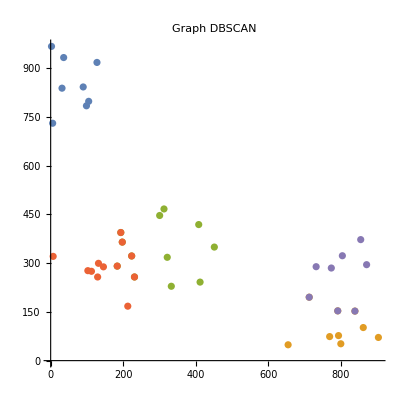

```mathematica
number=100;
cX=RandomReal[{0,1000},number];
cY=RandomReal[{0,1000},number];

points={};
For[i=1,i<=number,i++,
AppendTo[points,{cX[[i]],cY[[i]]}];
];

DBSCAN[points,150,8]
```